```mathematica
SetDirectory[NotebookDirectory[]];
Visual=Drop[ToExpression[ReadList["string.data",Word,RecordLists->True]],None,1];
```

```mathematica
ListAnimate[Table[ListPlot[Visual[[i]],PlotRange->{{0,100},{-1,1}}],{i,100}],5]
```

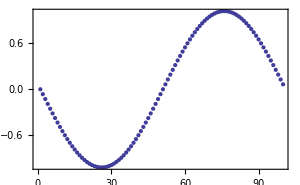

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
ListPlot[Visual[[5]],PlotRange->{{0,100},{-1,1}},Frame->True,ImageSize->300]
ListPlot[Visual[[24]],PlotRange->{{0,100},{-1,1}},Frame->True,ImageSize->300]
ListPlot[Visual[[42]],PlotRange->All,Frame->True,ImageSize->300]
ListPlot[Visual[[72]],PlotRange->All,Frame->True,ImageSize->300]
ListPlot[Visual[[92]],PlotRange->All,Frame->True,ImageSize->300]
```